x(t,β,ω0,C1,C2)=TraditionalForm`ⅇ^β\ (-t)\ (C1\ ⅇ^t\ √β^2 - ω0^2 + C2\ ⅇ^-t\ √β^2 - ω0^2)

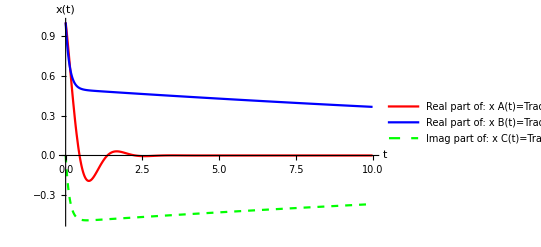

```mathematica
ClearAll[x];ClearAll[t];ClearAll[β];ClearAll[ω0];ClearAll[C1];ClearAll[C2];
ClearAll[graph ABC];
x[t_,β_,ω0_,C1_,C2_]:=(E^(-β*t))*((C1*E^(Sqrt[(β^2)-(ω0^2)]*t))+(C2*E^-(Sqrt[(β^2)-(ω0^2)]*t)));
"x(t,β,ω0,C1,C2)="<>ToString[x[t,β,ω0,C1,C2],TraditionalForm] 
x A:=x[t,0.5^-1,0.25^-1,0.5,0.5];
x B:=x[t,0.25^-1,2.0^-1,0.5,0.5];
x C:=x[t,0.25^-1,2.0^-1,-0.5I,0.5I];
graph ABC=Plot[{x A,x B,Im@x C},{t,0,10},PlotRange->Full,PlotStyle->{Red,Blue,{Green,Dashed}},PlotLegends->{
"Real part of: x A(t)="<>ToString[x A,TraditionalForm], 
"Real part of: x B(t)="<>ToString[x B,TraditionalForm],
"Imag part of: x C(t)="<>ToString[x C,TraditionalForm]}];
Show[graph ABC,PlotRange->{{0,10},{-0.5,1}},AxesLabel->{t,x[t]}]  (* N1a *)
```

```mathematica
ClearAll[t];ClearAll[β];ClearAll[ω0];ClearAll[C1];ClearAll[C2];
ClearAll[x D]; ClearAll[graph D];
x D[t_,C1_,C2_]:=x[t,0.35^-1,0.8^-1,C1,C2]
"x D(t)="<>ToString[x D[t,C1,C2],TraditionalForm]
graph D:=ContourPlot3D[x D[t,C1,C2],{t,0,10}, {C1,-10,10}, {C2,-10,10}];
Show[graph D,AxesLabel->{t,C1,C2}]
(* I believe the symmetry of the 4D graph below shows the principle that C1=C2≠0 *)
```

x D(t)=TraditionalForm`ⅇ^-2.85714\ t\ (C1\ ⅇ^2.5692\ t + C2\ ⅇ^-2.5692\ t)

-Graphics3D-

x E(t,C1)=TraditionalForm`ⅇ^-2.85714\ t\ (C1\ ⅇ^-2.5692\ t + C1\ ⅇ^2.5692\ t)

-Graphics3D-

USING TEST VALUE C1 = 1

x E(t,1)=TraditionalForm`ⅇ^-2.85714\ t\ (ⅇ^-2.5692\ t + ⅇ^2.5692\ t)

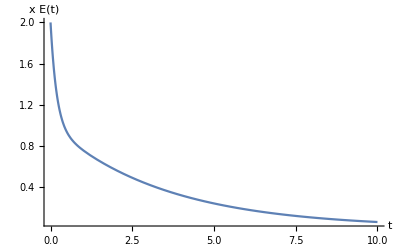

```mathematica
ClearAll[t];ClearAll[β];ClearAll[ω0];ClearAll[C1];ClearAll[C2];
ClearAll[x E]; ClearAll[graph E 2D];ClearAll[graph E 3D];
C1≠0;
C2:=C1;

x E[t_,C1_]:=x[t,0.35^-1,0.8^-1,C1,C2]; //Simplify

"x E(t,C1)="<>ToString[x E[t,C1],TraditionalForm]
graph E 3D:=Plot3D[x E[t,C1],{t,0,10},{C1,-10,10},PlotRange->Full];
Show[graph E 3D,AxesLabel->{t,"x E(t)","C1"}]

C1=1;  (* TEST VALUE!!! *)
"USING TEST VALUE C1 = " <> ToString[C1]
"x E(t,"<>ToString[C1]<>")="<>ToString[x E[t,C1],TraditionalForm]
graph E 2D:=Plot[x E[t,C1],{t,0,10},PlotRange->Full];
Show[graph E 2D,AxesLabel->{t,"x E(t)"}]
(* The 3D graph below shows x(t) for a range of C1 values; the 2D graph shows test value C1=1 *)
```

```mathematica
ClearAll[t];ClearAll[β];ClearAll[ω0];ClearAll[C1];ClearAll[C2];
ClearAll[t0 min]; ClearAll[x E dot];
C1≠0;
C2:=C1;

C1=1;   (* ANY NON-ZERO VALUE GIVES SAME RESULTS IN FindRoot[] *)
t0 min=FindRoot[x E[t,C1]==0,{t,0.0001}][[1,2]]; (* N1b *)
"t0 min="<>ToString[t0 min]<>"  <<<=== SMALLEST POSITIVE VALUE OF TIME FOR WHICH x(t)=0"
"x E(" <>ToString[t0 min]<>","<>ToString[C1]<>")="<>ToString[x E[t0 min,C1],TraditionalForm]<>
"  <<<=== CHECK: SHOULD BE VERY CLOSE TO ZERO"
```

t0 min=261.728  <<<=== SMALLEST POSITIVE VALUE OF TIME FOR WHICH x(t)=0

x E(261.728,1)=TraditionalForm`1.861417910207138`*^-33  <<<=== CHECK: SHOULD BE VERY CLOSE TO ZERO

```mathematica
ClearAll[t];ClearAll[β];ClearAll[ω0];ClearAll[C1];ClearAll[C2];
C1≠0;
C2:=C1;
x E dot[t_,C1_]=D[x E[t,C1],t];
"x E dot(t,"<>ToString[C1]<>")="<>ToString[x E dot[t,C1],TraditionalForm]
"x E dot(" <>ToString[t0 min]<>","<>ToString[C1]<>")="<>ToString[x E dot[t0 min,C1],TraditionalForm]<>
"  <<<=== SPEED AT TIME t0 min" (* N1b *)
```

x E dot(t,C1)=TraditionalForm`ⅇ^-2.85714\ t\ (2.5692\ C1\ ⅇ^2.5692\ t - 2.5692\ C1\ ⅇ^-2.5692\ t) - 2.85714\ ⅇ^-2.85714\ t\ (C1\ ⅇ^-2.5692\ t + C1\ ⅇ^2.5692\ t)

x E dot(261.728,C1)=TraditionalForm`-5.3599×10^-34\ C1  <<<=== SPEED AT TIME t0 min